P(l<L)

```mathematica
P11[l_,γ_]:=(1-1/(1+γ))* (1/(1+γ))^l
```

P(l=L)

```mathematica
P12[L_,γ_]:=(1/(1+γ))^L
```

```mathematica
ENO[L_,γ_]:=-(Sum[P11[l,γ]*Log[2,P11[l,γ]],{l,0,L-1}]+(1/(1+γ))^L*Log[2,(1/(1+γ))^L])
```

PARTIALLY ORDERED

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+c*γ))^(l1+l2)((c*γ)/(2+c*γ))^c

P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*(c*γ)^c/(c*γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*(c*γ)^c/(c*γ+2)^(l1+l2+c),{l2,0,L2-1}]

P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]

ENPO[L1_,L2_,c_,γ_]:=-Sum[Sum[P1[l1,l2,c,γ]*Log[2,P1[l1,l2,c,γ]],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ]*Log[2, P2[l1,L2,c,γ]],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ]*Log[2, P2[l2,L1,c,γ]],{l2,0,L2-1}]-P3[L1,L2,c,γ]*Log[2, P3[L1,L2,c,γ]]
```

```mathematica
ENPO2[B_,L1_,L2_,c_,γ_]:=-Sum[P11[l,γ]*Log[2,P11[l,γ]],{l,0,B-1}]-Sum[Sum[P12[B,γ]*P1[l1,l2,c,γ]*Log[2,P12[B,γ]*P1[l1,l2,c,γ]],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P12[B,γ]*P2[l1,L2,c,γ]*Log[2, P12[B,γ]*P2[l1,L2,c,γ]],{l1,0,L1-1}]-Sum[P12[B,γ]*P2[l2,L1,c,γ]*Log[2, P12[B,γ]*P2[l2,L1,c,γ]],{l2,0,L2-1}]-P12[B,γ]*P3[L1,L2,c,γ]*Log[2, P12[B,γ]*P3[L1,L2,c,γ]]
```

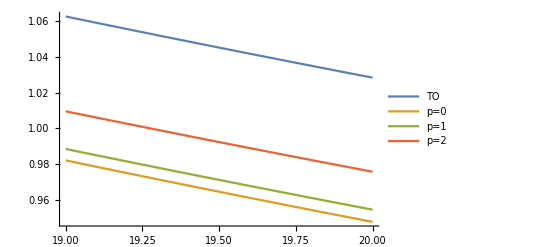

```mathematica
Plot[{ENO[4,1/x],ENPO[3,1,1,1/x],ENPO2[1,2,1,1,1/x],ENPO2[2,1,1,1,1/x]},{x,19,20},PlotLegends->{"TO","p=0","p=1","p=2"}]
```

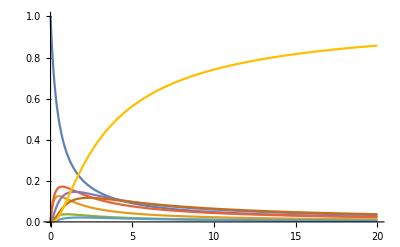

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+c*γ))^(l1+l2)((c*γ)/(2+c*γ))^c

P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*(c*γ)^c/(c*γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*(c*γ)^c/(c*γ+2)^(l1+l2+c),{l2,0,L2-1}]

P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
Plot[{P1[0,0,1,1/x],P1[1,0,1,1/x], P1[2,0,1,1/x],P2[0,1,1,1/x], P2[1,1,1,1/x], P2[2,1,1,1/x], P2[0,3,1,1/x], P3[3,1,1,1/x]},{x,0,20}, PlotRange->{0,1}]
with
```

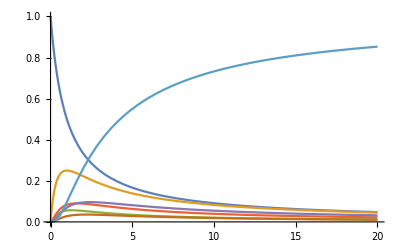

```mathematica
Plot[{P11[0,1/x],P11[1,1/x], P12[1,1/x]*P1[1,0,1,1/x],P12[1,1/x]*P2[0,1,1,1/x], P12[1,1/x]*P2[1,1,1,1/x], P12[1,1/x]*P2[0,2,1,1/x],P12[1,1/x]* P3[2,1,1,1/x]},{x,0,20}, PlotRange->{0,1}]
```

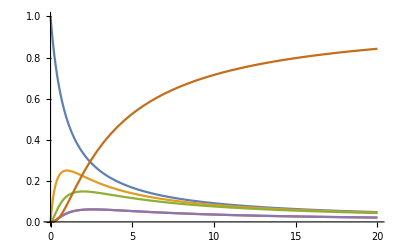

```mathematica
Plot[{P11[0,1/x],P11[1,1/x],P11[2,1/x], P12[2,1/x]*P2[0,1,1,1/x],P12[2,1/x]*P2[0,1,1,1/x],P12[2,1/x]* P3[1,1,1,1/x] },{x,0,20}, PlotRange->{0,1}]
```